seems to be functioning! is it the boundary conditions that fuck it up?

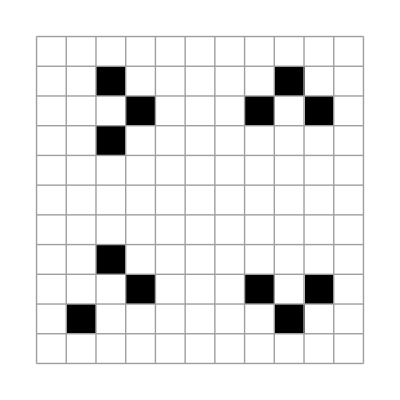
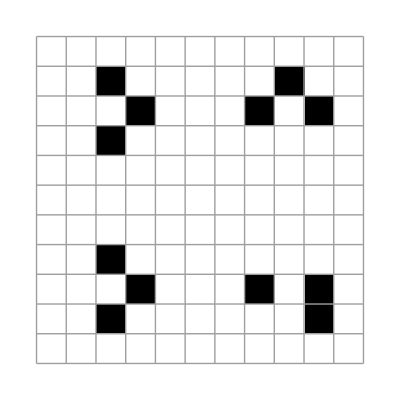
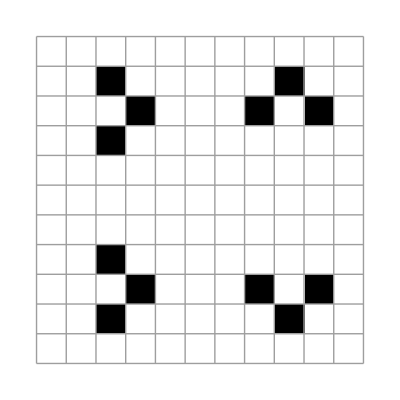
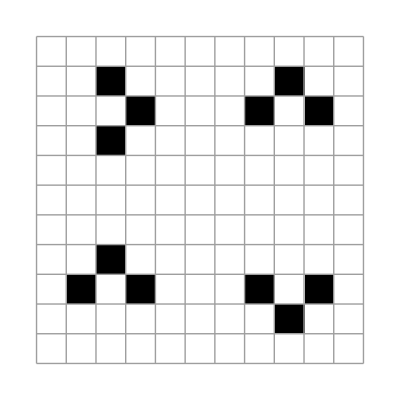

```mathematica
Get["/Users/johncosnett/Dropbox/05_PROGRAMS/001_LIFE/05_four_maybe_it_works.m"];
looker2=plt[({{0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, xNW11, xN11, xNE11, 0, 0, 0, xNW12, xN12, xNE12, 0}, {0, xW11, x11, xE11, 0, 0, 0, xW12, x12, xE12, 0}, {0, xSW11, xS11, xSE11, 0, 0, 0, xSW12, xS12, xSE12, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, xNW21, xN21, xNE21, 0, 0, 0, xNW22, xN22, xNE22, 0}, {0, xW21, x21, xE21, 0, 0, 0, xW22, x22, xE22, 0}, {0, xSW21, xS21, xSE21, 0, 0, 0, xSW22, xS22, xSE22, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}})/.#]&;
(*X0=IntegerPart@ImageData@(looker2/@endGame)[[1]];*)

looker2/@endGame
```

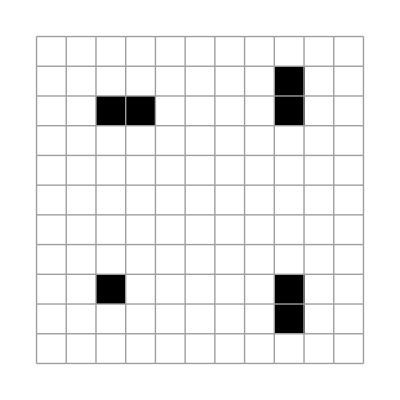
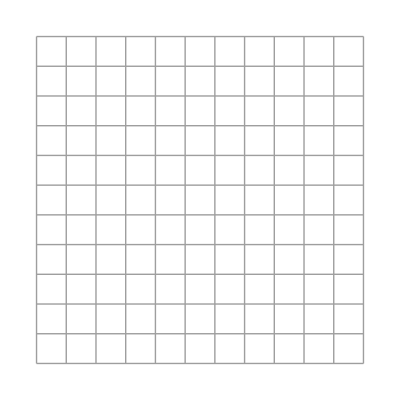
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
X0=({{0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, xNW11, xN11, xNE11, 0, 0, 0, xNW12, xN12, xNE12, 0}, {0, xW11, x11, xE11, 0, 0, 0, xW12, x12, xE12, 0}, {0, xSW11, xS11, xSE11, 0, 0, 0, xSW12, xS12, xSE12, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, xNW21, xN21, xNE21, 0, 0, 0, xNW22, xN22, xNE22, 0}, {0, xW21, x21, xE21, 0, 0, 0, xW22, x22, xE22, 0}, {0, xSW21, xS21, xSE21, 0, 0, 0, xSW22, xS22, xSE22, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}})/.endGame[[1]];
plt/@NestList[updateLife2[{11,11}][ #]&,
X0,3]
```

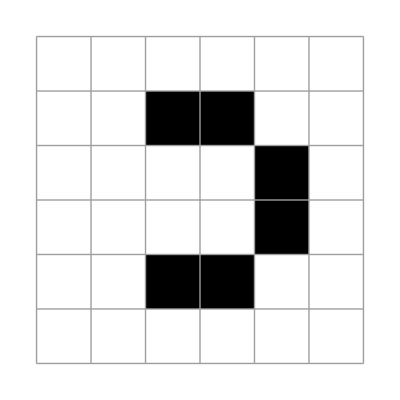
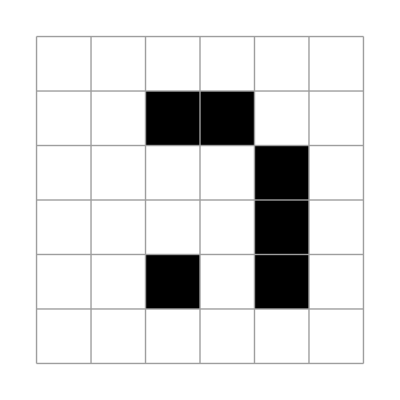
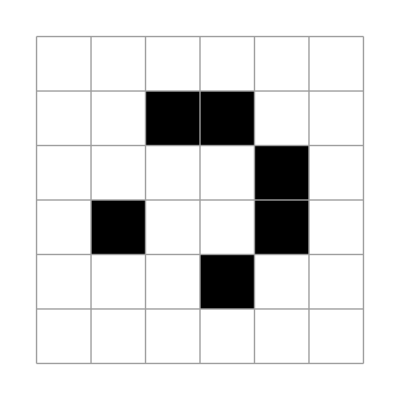
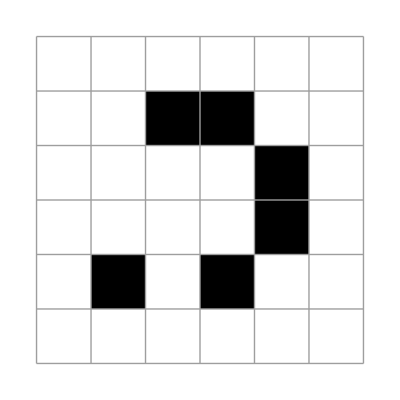

```mathematica
Get["/Users/johncosnett/Dropbox/05_PROGRAMS/001_LIFE/05_four_maybe_it_works.m"];
looker2=plt[({{0, 0, 0, 0, 0, 0}, {0, xNW11, xN11, xN12, xNE12, 0}, {0, xW11, x11, x12, xE12, 0}, {0, xW21, x21, x22, xE22, 0}, {0, xSW21, xS21, xS22, xSE22, 0}, {0, 0, 0, 0, 0, 0}})/.#]&;
(*X0=IntegerPart@ImageData@(looker2/@endGame)[[1]];*)

looker2/@endGame
```

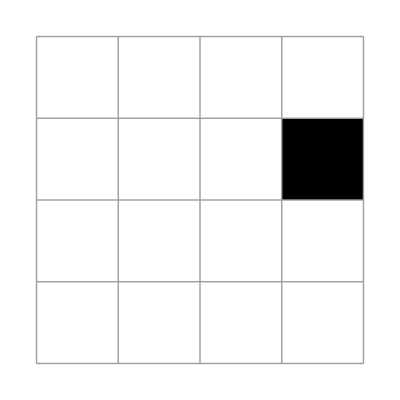
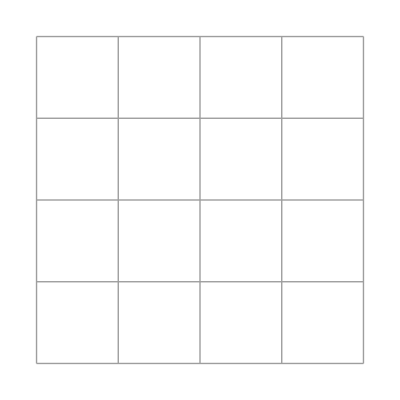
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
X0=({{0, 0, 0, 0, 0, 0}, {0, xNW11, xN11, xN12, xNE12, 0}, {0, xW11, x11, x12, xE12, 0}, {0, xW21, x21, x22, xE22, 0}, {0, xSW21, xS21, xS22, xSE22, 0}, {0, 0, 0, 0, 0, 0}})/.endGame[[1]];
plt/@NestList[updateLife2[{4,4}][ #]&,
X0,3]
```